## Mobius matrix of graph - not a full one

```mathematica
allGraphs5[K5Key,"colofour"]
```

v1x2x3x4x5

```mathematica
Keys5[colofour_]:=Keys5[colofour]=Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,colofour]]]==1&]
```

```mathematica
Vars5[colofour_]:=Vars5[colofour]=Sort[Table[allGraphs5[k,colofour],{k,Keys5[colofour]}],CompareSymbols]
```

```mathematica
MobiusGraph4Colofour[key_,allGraphs_,colofour_]:=Block[{form=allGraphs[key,colofour], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Keys5[colofour],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];
(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,colofour]===v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue], Style[DropMore[n,3],Red]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
MobiusGraph4ColofourRev[key_,allGraphs_,colofour_]:=Block[{form=allGraphs[key,colofour], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Keys5[colofour],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];
(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,colofour]===v&]]];
found [v]=set;
c=SymbolLevel[set[colofour]];
set=SymbolToSets[set[colofour]];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
from[[1]],
to [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
allGraphs5[K4Key,"colofourgenerator"]
```

g12x3x4x5+g13x2x4x5+g14x2x3x5+g15x2x3x4-3 g1x2x3x4x5

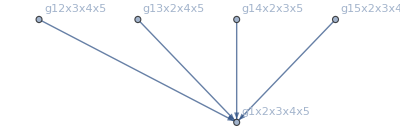

```mathematica
MobiusGraph4ColofourRev[K4Key,allGraphs5,"colofourgenerator"]
```

```mathematica
allGraphs5[K4Key,allGraphs5,"colofournull"]
```

Missing[KeyAbsent,<|0→<|signature→0,matrix→{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4},{5}},vertices→{1,2,3,4,5},edges→{},relations→{x0==x19683+x39366,x0==x13122+x6561,x0==x2187+x4374,x0==x1458+x729,x0==x243+x486,x0==x162+x81,x0==x27+x54,x0==x18+x9,x0==x3+x6,x0==x1+x2},links→{},6,colofournull→p1x2x3x4x5,colofourrealnull→n1x2x3x4x5,atleast→34,atleastwhy→Propagate from relation {9, 18} with values {21, 13},embed→628,colofourgenerator→g12345,colotree→t12345+t1234x5+t123x45+t123x4x5+t12x345+t12x34x5+t12x3x45+t12x3x4x5+t1x2345+t1x234x5+t1x23x45+t1x23x4x5+t1x2x345+t1x2x34x5+t1x2x3x45+t1x2x3x4x5|>,19683→<|1|>,1892,2→<|1|>|>]
 |  |  |  |

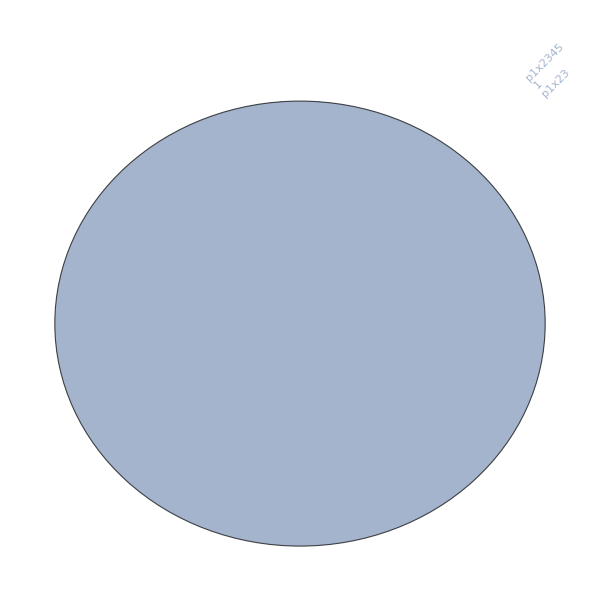

```mathematica
MobiusGraph4Colofour[K4Key,allGraphs5,"colofournull"]
```

```mathematica
PartialMobius[k_,colofour_:"colofourrealnull"]:=Block[{
allPartitions=Vars5[colofour],
result=Association[],
vars=ReverseSort[ ListofVars[allGraphs5[k,colofour]],CompareSymbols],
mobius =Graph[MobiusGraph4Colofour[k,allGraphs5,colofour],ImageSize->Small],
outvertices
},
(* initialize the result.  This is a two dimensional dictionary with partition symbols as keys *)
Table[result[p]=Association[];Table[result[p,p2]=0,{p2,allPartitions}],{p,allPartitions}];

(* all variables that occur have a 1 at the diagonal *)
Table[result[v,v]=1,{v,vars}];
(*Print[vars,mobius];*)

(* now for every var we compute the mobius using the mobius graph *)
vars=Rest[vars];(* head is 0 element of the lattice *)
Table[
outvertices=Select[VertexOutComponent[mobius,v],#=!=v&];
(*outvertices=Select[outvertices,SymbolLevel[#]==SymbolLevel[v]-1&];*)
(*Print[v->outvertices];*)
Table[result[v,p]=-Total[Table[result[v2,p],{v2,outvertices}]],{p,Select[allPartitions,#=!=v&]}];
,
{v,vars}
];

(* compute the result.  Keys that don't exist have value 0 *)
Table[If[!KeyExistsQ[result[p1],p2],0,result[p1,p2]],{p1,allPartitions},{p2,allPartitions}]
]
```

```mathematica
PartialMobiusRev[k_,colofour_:"colofourgenerator"]:=Block[{
allPartitions=Vars5[colofour],
result=Association[],
vars=ReverseSort[ ListofVars[allGraphs5[k,colofour]],CompareSymbols],
mobius =Graph[MobiusGraph4ColofourRev[k,allGraphs5,colofour],ImageSize->Small],
outvertices
},
(* initialize the result.  This is a two dimensional dictionary with partition symbols as keys *)
Table[result[p]=Association[];Table[result[p,p2]=0,{p2,allPartitions}],{p,allPartitions}];

(* all variables that occur have a 1 at the diagonal *)
Table[result[v,v]=1,{v,vars}];
(*Print[vars,mobius];*)

(* now for every var we compute the mobius using the mobius graph *)
vars=Rest[vars];(* head is 0 element of the lattice *)
Table[
outvertices=Select[VertexOutComponent[mobius,v],#=!=v&];
(*outvertices=Select[outvertices,SymbolLevel[#]==SymbolLevel[v]-1&];*)
(*Print[v->outvertices];*)
Table[result[v,p]=-Total[Table[result[v2,p],{v2,outvertices}]],{p,Select[allPartitions,#=!=v&]}];
,
{v,vars}
];

(* compute the result.  Keys that don't exist have value 0 *)
Table[If[!KeyExistsQ[result[p1],p2],0,result[p1,p2]],{p1,allPartitions},{p2,allPartitions}]
]
```

```mathematica
MobiusMatrix[allGraphs5]==PartialMobius[K5Key]
```

True

```mathematica
EulerCharacteristic[k_,colofour_:"colofourgenerator"]:=Block[{zero,one,mat,i},
mat=PartialMobius[k,colofour];
For[i=1,i<=Length[mat],i++,
If[mat[[i,i]]≠0,one=i;Break[]]
];
For[i=Length[mat],i≥ 1,i--,
If[mat[[i,i]]≠0,zero=i;Break[]]
];
mat[[one,zero]]
]
```

```mathematica
EulerCharacteristic[1,"colofour"]
```

-6

```mathematica
Table[col->{Length[ListofVars[allGraphs5[lambdaKey,col]]],Length[ListofVars[allGraphs5[starKey,col]]],EulerCharacteristic[lambdaKey,col],EulerCharacteristic[starKey,col]},{col,{"colofour","colofournull","colofourgenerator","colotree"}}]
```

{colofour→{11,11,1,1},colofournull→{26,26,0,0},colofourgenerator→{11,11,0,0},colotree→{4,28,0,0}}

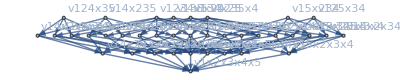
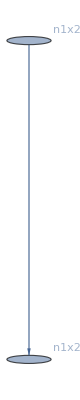
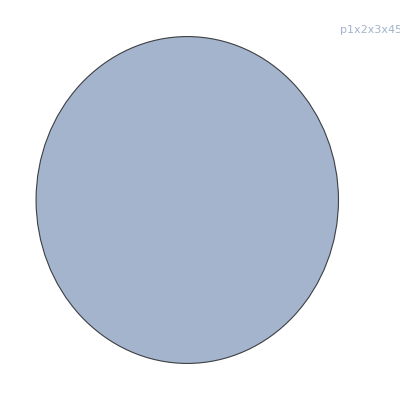
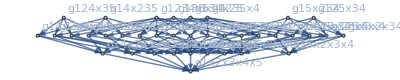
{v1234x5+v1235x4+v123x4x5+v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5→-Graphics-,-n1x2x3x45+n1x2x3x4x5→-Graphics-,p1x2x3x45→-Graphics-,g1234x5+g1235x4-g123x4x5+g124x35-g124x3x5+g125x34-g125x3x4-g12x34x5-g12x35x4+2 g12x3x4x5+g134x25-g134x2x5+g135x24-g135x2x4-g13x24x5-g13x25x4+2 g13x2x4x5+g14x235-g14x23x5-g14x25x3-g14x2x35+2 g14x2x3x5+g15x234-g15x23x4-g15x24x3-g15x2x34+2 g15x2x3x4-g1x234x5-g1x235x4+2 g1x23x4x5-g1x24x35+2 g1x24x3x5-g1x25x34+2 g1x25x3x4+2 g1x2x34x5+2 g1x2x35x4-6 g1x2x3x4x5→-Graphics-}

```mathematica
With[
{k=1},
Table[allGraphs5[k,col]->MobiusGraph4ColofourRev[k,allGraphs5,col],{col,{"colofour","colofourrealnull","colofournull","colofourgenerator"}}]
]
```

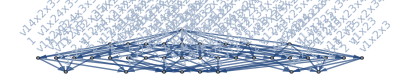
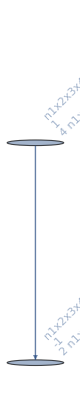
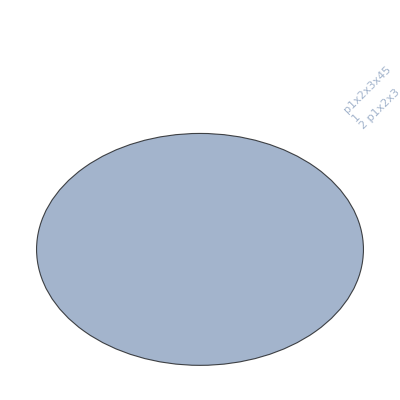
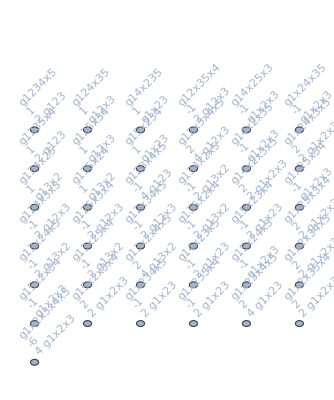
{v1234x5+v1235x4+v123x4x5+v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5→-Graphics-,-n1x2x3x45+n1x2x3x4x5→-Graphics-,p1x2x3x45→-Graphics-,g1234x5+g1235x4-g123x4x5+g124x35-g124x3x5+g125x34-g125x3x4-g12x34x5-g12x35x4+2 g12x3x4x5+g134x25-g134x2x5+g135x24-g135x2x4-g13x24x5-g13x25x4+2 g13x2x4x5+g14x235-g14x23x5-g14x25x3-g14x2x35+2 g14x2x3x5+g15x234-g15x23x4-g15x24x3-g15x2x34+2 g15x2x3x4-g1x234x5-g1x235x4+2 g1x23x4x5-g1x24x35+2 g1x24x3x5-g1x25x34+2 g1x25x3x4+2 g1x2x34x5+2 g1x2x35x4-6 g1x2x3x4x5→-Graphics-}

```mathematica
With[
{k=1},
Table[allGraphs5[k,col]->MobiusGraph4Colofour[k,allGraphs5,col],{col,{"colofour","colofourrealnull","colofournull","colofourgenerator"}}]
]
```

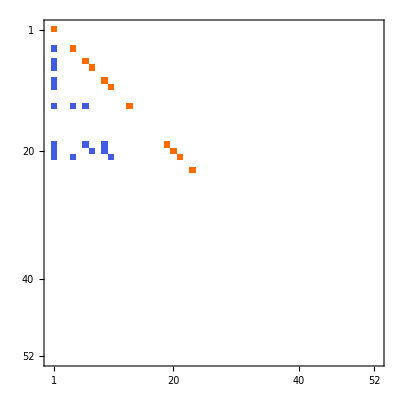
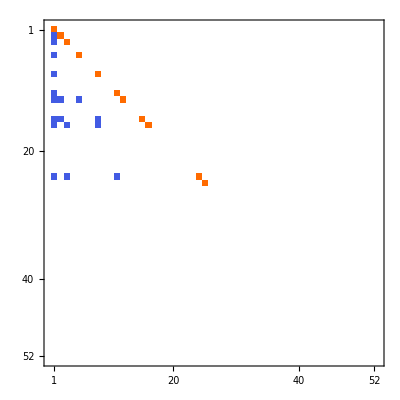
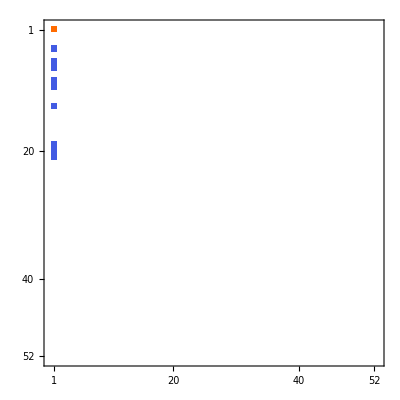
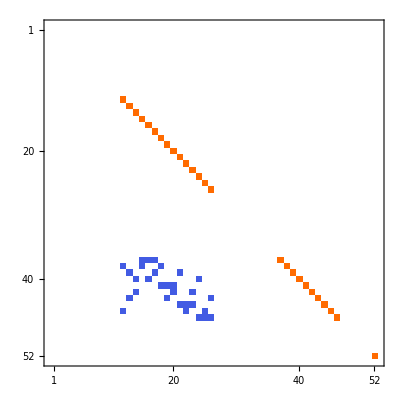
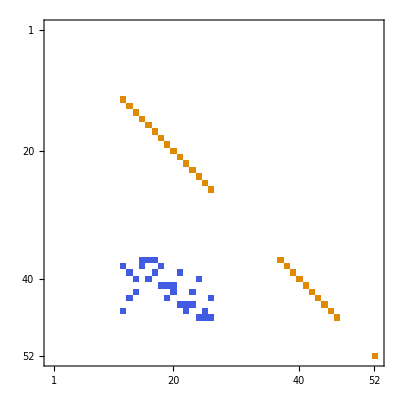
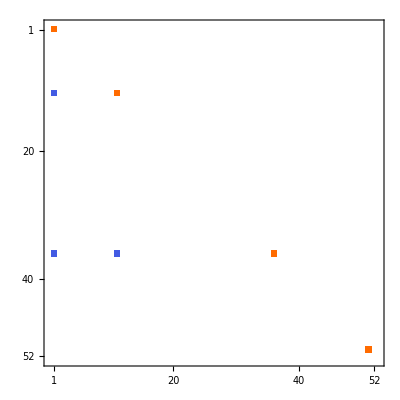
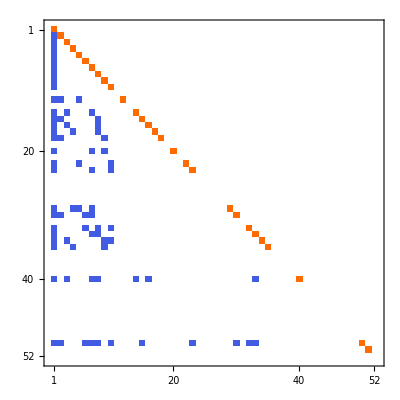
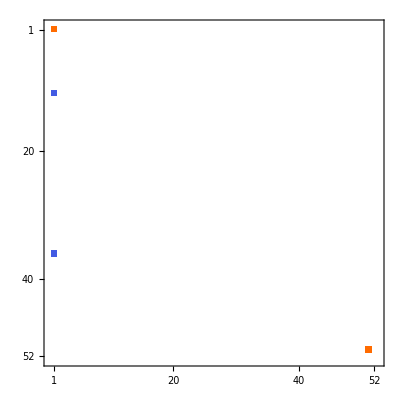
{colofour→{11,11,-Graphics-,-Graphics-,-Graphics-},colofournull→{26,26,-Graphics-,-Graphics-,-Graphics-},colofourgenerator→{11,11,-Graphics-,-Graphics-,-Graphics-},colotree→{4,28,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[col->{Length[ListofVars[allGraphs5[lambdaKey,col]]],Length[ListofVars[allGraphs5[starKey,col]]],MatrixPlot[PartialMobiusRev[lambdaKey,col]],MatrixPlot[PartialMobiusRev[starKey,col]],MatrixPlot[PartialMobiusRev[lambdaKey,col].PartialMobiusRev[starKey,col]]},{col,{"colofour","colofournull","colofourgenerator","colotree"}}]
```

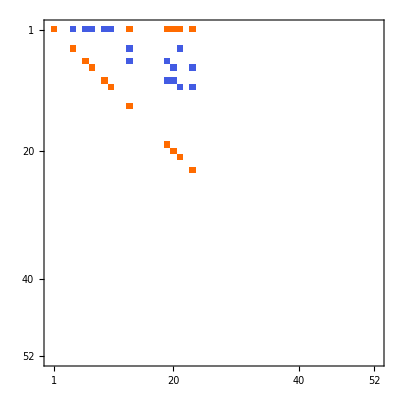
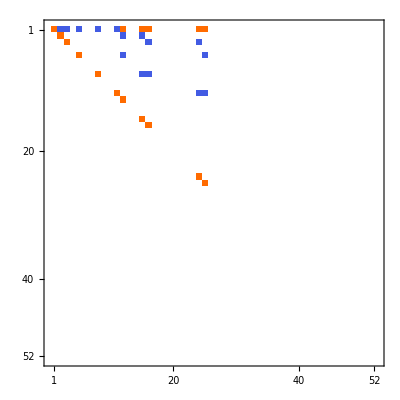
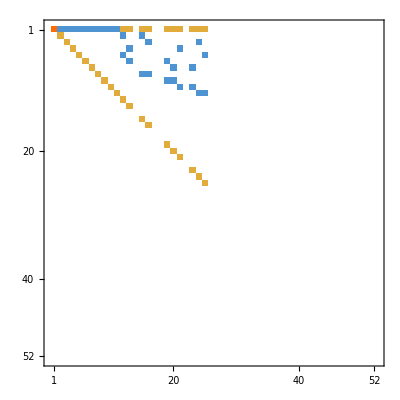
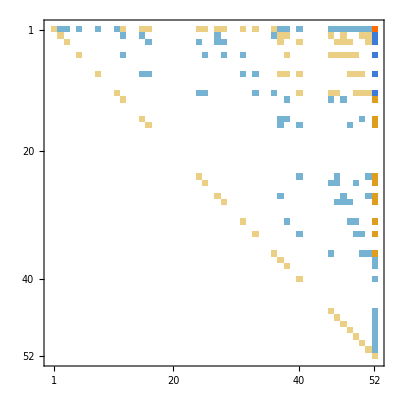
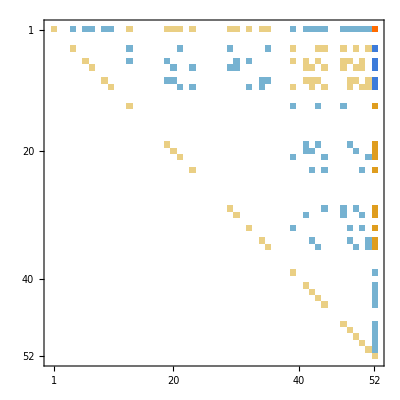
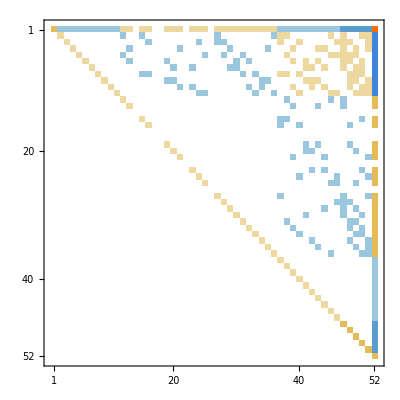
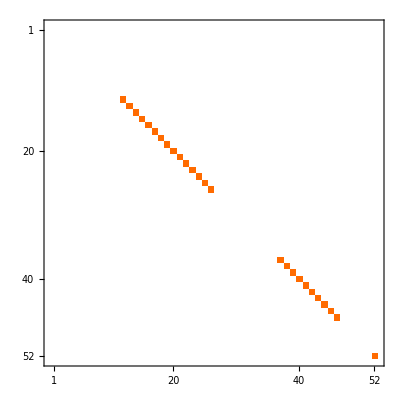
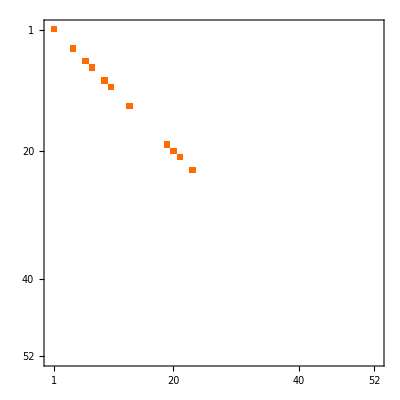
{colofour→{11,11,-Graphics-,-Graphics-,-Graphics-},colofourrealnull→{27,27,-Graphics-,-Graphics-,-Graphics-},colofournull→{26,26,-Graphics-,-Graphics-,-Graphics-},colofourgenerator→{11,11,-Graphics-,-Graphics-,-Graphics-},colotree→{4,28,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[col->{Length[ListofVars[allGraphs5[lambdaKey,col]]],Length[ListofVars[allGraphs5[starKey,col]]],MatrixPlot[PartialMobius[lambdaKey,col]],MatrixPlot[PartialMobius[starKey,col]],MatrixPlot[PartialMobius[lambdaKey,col]+PartialMobius[starKey,col]]},{col,{"colofour","colofourrealnull","colofournull","colofourgenerator","colotree"}}]
```

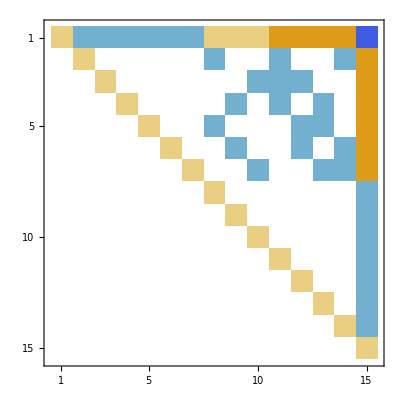

```mathematica
MobiusMatrix[allGraphs4]//MatrixPlot
```

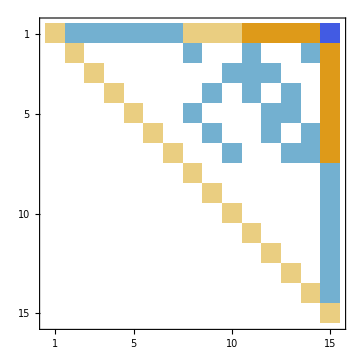

```mathematica
Transpose[Select[Transpose[Select[PartialMobius[K4Key,"colofourrealnull"],#≠Table[0,{k,52}]&]],#≠Table[0,{k,15}]&]]//MatrixPlot
```

```mathematica
ChildMob[k_,colofour_:"colofourrealnul"]:=Labeled[MatrixPlot[PartialMobius[k,colofour]],k]->Table[Table[Labeled[MatrixPlot[PartialMobius[child,colofour]],child],{child,childCouple}],{childCouple,allGraphs5[k,"children"]}]
```

```mathematica
allGraphs5[0,"children"]
```

{{19683,39366},{6561,13122},{2187,4374},{729,1458},{243,486},{81,162},{27,54},{9,18},{3,6},{1,2}}

```mathematica
Solve[PartialMobius[0]==a PartialMobius[19683]+  PartialMobius[39366],{a}]
```

{}

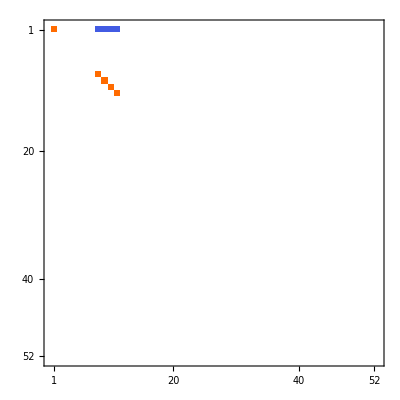
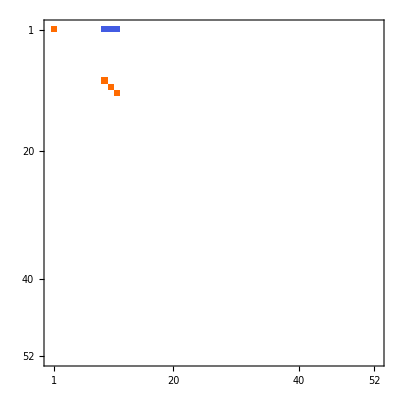
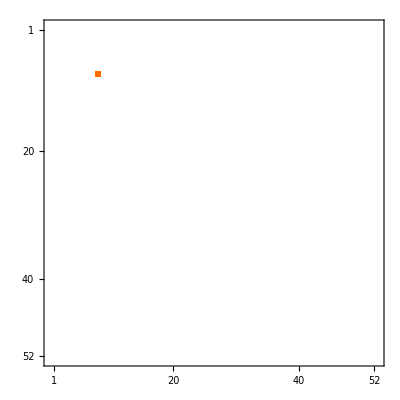
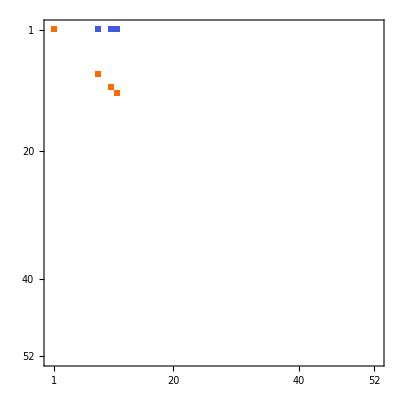
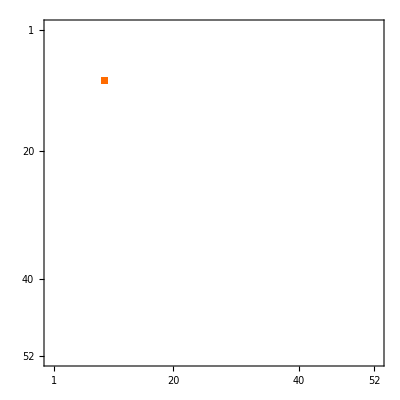
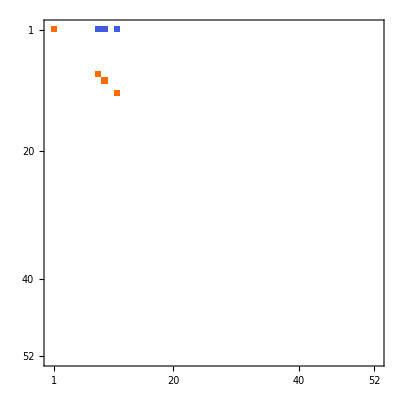
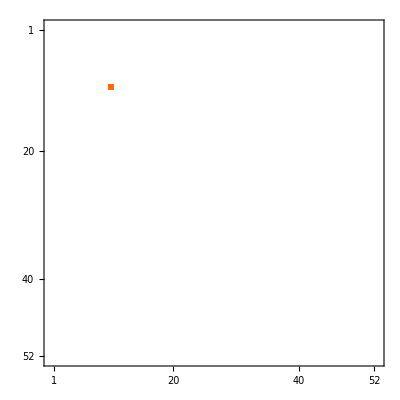
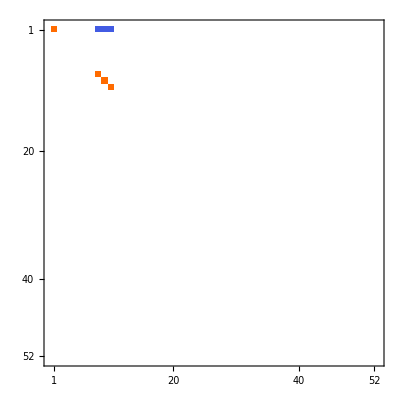
-Graphics-364→{{-Graphics-20047,-Graphics-49207},{-Graphics-6925,-Graphics-36085},{-Graphics-2551,-Graphics-31711},{-Graphics-1093,-Graphics-30253}}

```mathematica
ChildMob[K4Key,"colofour"]
```

```mathematica
ChildMob2[k_,colofour_:"colofour"]:=EulerCharacteristic[k,colofour]->Table[Table[EulerCharacteristic[child,colofour],{child,childCouple}],{childCouple,allGraphs5[k,"children"]}]
```

```mathematica
ChildMob2[1,"colofour"]
```

-6→{{-2,2},{-2,2},{-6,2},{-6,2},{-2,2},{-6,2},{-6,2},{-6,2},{-6,2}}

```mathematica
ChildMob3[k_]:=k->TrianglesInGraph[allGraphs5[k,"graph"]]->Flatten[Table[Differences[Table[TrianglesInGraph[allGraphs5[child,"graph"]],{child,childCouple}]],{childCouple,allGraphs5[k,"children"]}]]
```

```mathematica
ChildMob3[K4Key]
```

364→4→{1,1,1,1}

```mathematica
ChildMob3[lambdaKey]
```

20665→0→{1,1,1,1,1}

```mathematica
ChildMob3[starKey]
```

8859→0→{1,1,1,1,1}

```mathematica
Table[ChildMob3[k],{k,RandomSample[Keys[allGraphs5],20]}]
```

{29442→5→{-3,-3},25138→1→{-1,-1,-1},41646→0→{-1,1,-1,1,-1},14044→0→{-1,-1,-1,-1},26609→2→{-3,-3},27229→3→{-3,0,-3},3727→0→{-1,0,0,-1,0,0},22140→0→{-1,-1,-1,1,-1,1},21952→1→{0,-1,0,-1,0,0},9558→0→{-1,1,1,-1,-1,-1},9057→1→{-1,-1,-1,-1},28794→5→{-3,-3},28548→2→{-1,-2,2,-1},13122→0→{0,0,0,0,0,0,0,0,0},7573→3→{-3,-3,-3},22114→0→{-1,-1,-1,1,1,0},21901→0→{2,-2,0,-2,0},19710→0→{0,0,-1,0,0,0,0,0},29190→2→{-2,-1,-1,-1},27001→1→{-1,-1,-1,2,-1}}

```mathematica
ChildMob4[k_]:=ShowGraph5Least[k]->Table[Table[ShowGraph5Least[child],{child,childCouple}],{childCouple,allGraphs5[k,"children"]}]
```

```mathematica
ChildMob3[22603]
```

22603→1→{-1,2,-1,-1,-1}

```mathematica
ChildMob2[22603]
```

2→{{2,-1},{1,-1},{1,-1},{2,-1},{1,-1}}

```mathematica
ChildMob3[22603]
```

22603→1→{-1,2,-1,-1,-1}

## Parents and children

```mathematica
DoParentChild[key_,action_]:=action[key]->Table[Table[action[child],{child,children}],{children,allGraphs5[key,"children"]}]
```

```mathematica
Bases["C"]
```

<|Colofour→colofour,AtomKeys→{29524,29525,29533,29527,29767,29605,29551,49207,36085,31711,30253,29768,29608,29560,49208,49216,49210,36086,36166,36112,31714,31954,31738,30262,30496,30334,29537,29857,29797,29633,56011,51475,49963,38281,36817,32441,49220,56012,51478,49972,36194,38308,36898,31984,32684,30586,29888,58288,56770,52232,39014,59048},Variables→{v1x2x3x4x5,v1x2x3x45,v1x2x34x5,v1x2x35x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x45,v1x24x35,v1x25x34,v12x3x45,v12x34x5,v12x35x4,v13x2x45,v13x24x5,v13x25x4,v14x2x35,v14x23x5,v14x25x3,v15x2x34,v15x23x4,v15x24x3,v1x2x345,v1x234x5,v1x235x4,v1x245x3,v123x4x5,v124x3x5,v125x3x4,v134x2x5,v135x2x4,v145x2x3,v12x345,v123x45,v124x35,v125x34,v13x245,v134x25,v135x24,v14x235,v145x23,v15x234,v1x2345,v1234x5,v1235x4,v1245x3,v1345x2,v12345}|>

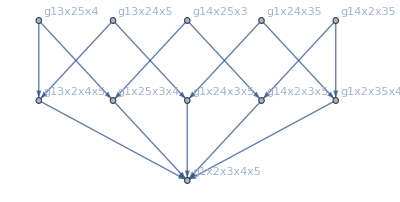
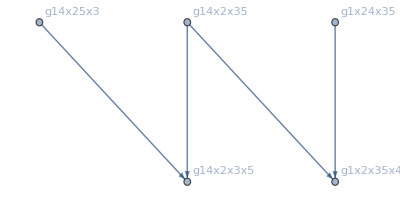
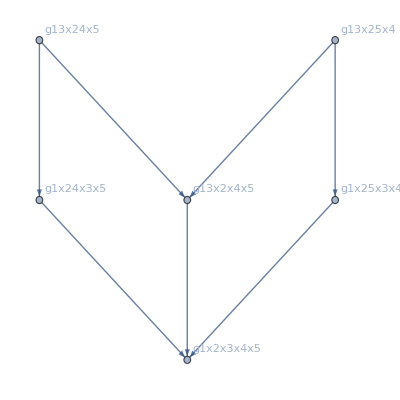
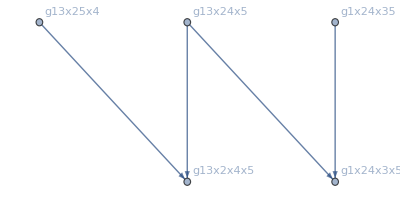
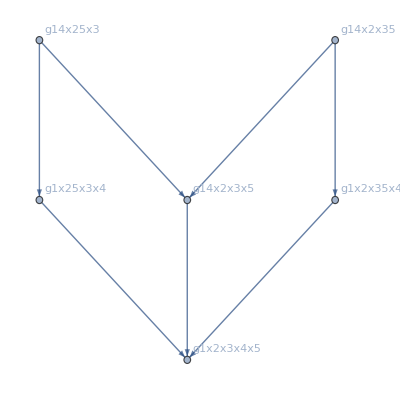
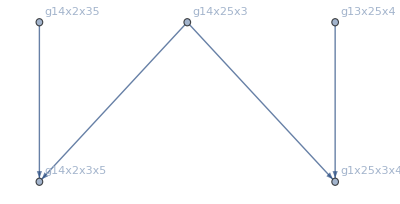
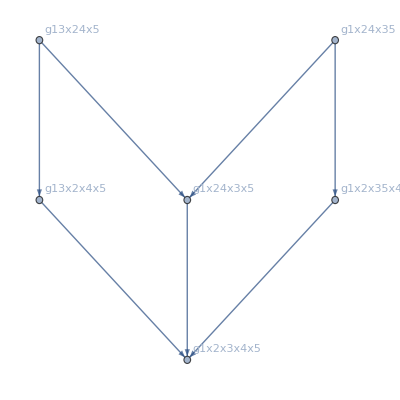
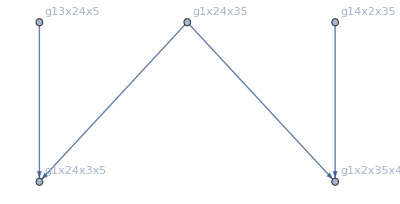
-Graphics--Graphics-206653→-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820--Graphics-295210--Graphics-294970--Graphics-294430--Graphics-273370--Graphics-229630+-Graphics-295240→{{-Graphics--Graphics-272262→-Graphics-294400+-Graphics-273340+-Graphics-273100--Graphics-295210--Graphics-273370,-Graphics--Graphics-359771→-Graphics-229360+-Graphics-228820--Graphics-294970--Graphics-294430--Graphics-229630+-Graphics-295240},{-Graphics--Graphics-228522→-Graphics-294400+-Graphics-229360+-Graphics-228820--Graphics-294430--Graphics-229630,-Graphics--Graphics-316811→-Graphics-273340+-Graphics-273100--Graphics-295210--Graphics-294970--Graphics-273370+-Graphics-295240},{-Graphics--Graphics-207462→-Graphics-273340+-Graphics-273100+-Graphics-229360--Graphics-294970--Graphics-273370,-Graphics--Graphics-230411→-Graphics-294400+-Graphics-228820--Graphics-295210--Graphics-294430--Graphics-229630+-Graphics-295240},{-Graphics--Graphics-206922→-Graphics-294400+-Graphics-273340+-Graphics-228820--Graphics-295210--Graphics-294430,-Graphics--Graphics-208031→-Graphics-273100+-Graphics-229360--Graphics-294970--Graphics-273370--Graphics-229630+-Graphics-295240},{-Graphics--Graphics-206682→-Graphics-273100+-Graphics-229360+-Graphics-228820--Graphics-294970--Graphics-229630,-Graphics--Graphics-272591→-Graphics-294400+-Graphics-273340--Graphics-295210--Graphics-294430--Graphics-273370+-Graphics-295240}}

```mathematica
With[{base="G"},
DoParentChild[lambdaKey,Labeled[Graph[MobiusGraph4ColofourRev[#,allGraphs5,Bases[base,"Colofour"]],ImageSize->400],ShowGraph5Least[#]->(allGraphs5[#,Bases[base,"Colofour"]]/.RepGraph[base])]&]
]
```

```mathematica
DoParentChild[0,allGraphs5[#,"graph"]&]
```